## Code to analyze an art shape to make on the laser cutter

## Some tools to manipulate polygons

```mathematica
(* get vertex coords *)
verts[shape_] := PolyhedronData[shape,"Faces"][[1]]
```

```mathematica
(* get poly indices into verts *)
polys[shape_] := PolyhedronData[shape,"Faces"][[2,1]]
```

```mathematica
toPolys[shape_] := verts[shape][[#]]& /@ polys[shape]
```

```mathematica
(* centroid of a polygon : VALID FOR N-GON, NOT GENERAL CASE *)
centroid[poly_] := Total[poly]/Length[poly]
```

```mathematica
(* compute the unit normal to a polygon *)
normal[poly_] := #/Norm[#]&[Cross[poly[[1]]-poly[[2]],poly[[2]]-poly[[3]]]]
```

```mathematica
(* create a notch in a polygon of the required gap, centered at an edge, of the given depth to the centroid *)
notch[poly_, gap_, depth_] := Module[{a,b,c,d,e,f,m,i,n,pts,length,ctr,r,mid},
ctr = centroid[poly];
n = Length[poly];
pts = {};
For[i=1,i≤n,i++,
a=poly[[i]];
f=poly[[Mod[i+1,n,1]]];
mid = (a+f)/2; (* midpoint *)
length = Norm[f-a]; (* edge length *)
r = (length-gap)/length/2; (* ratio to where notch starts *)
b = a+(f-a)*r;
e = f+(a-f)*r;
c = b + depth(ctr-mid)/Norm[ctr-mid];
d = e + depth(ctr-mid)/Norm[ctr-mid];

(* add the points, except the last one, which is added next pass *)
AppendTo[pts,a];
If[OddQ[i],
AppendTo[pts,b];
AppendTo[pts,c];
AppendTo[pts,d];
];
AppendTo[pts,e];
]; (*For*)
Return[pts];
]
```

Start with this shape

```mathematica
PolyhedronData["GreatRhombicosidodecahedron"]
```

-Graphics3D-

-Graphics3D-

```mathematica
(* select those polygons with not 10 sides *)
pg = Select[toPolys["GreatRhombicosidodecahedron"],Length[#]≠10&]*2;
Graphics3D[Polygon /@ pg]
```

-Graphics3D-

```mathematica
(* obtain side length *)
sideLength = Simplify[Norm[pg[[1,1]]-pg[[1,2]]]]
```

2

```mathematica
(* separate the polygons *)
hexes = Select[pg,Length[#]==6&];
squares= Select[pg,Length[#]==4&];
```

```mathematica
(* count number of each type of poly *)
Tally[Length/@pg]
```

{{6,20},{4,30}}

```mathematica
(* find 2 padjacent pieces *)
pg2 = {pg[[4]],pg[[7]]};
Graphics3D[Polygon/@pg2]
```

-Graphics3D-

```mathematica
(* angle between them *)
{n1,n2} = normal /@ pg2;
angle = Simplify[ArcCos[(n1.n2)/(Norm[n1]Norm[n2])] ]
```

ArcCos[(1+√5)/(2 √3)]

```mathematica
N[angle]
```

0.364864

```mathematica
(* radius to each type of polygon *)
dists := Simplify[Norm /@ centroid /@ pg2];
(* distance to each type of poly. Note hex dist < square dist *)
{sqDist,hexDist} =Simplify[ {Max[dists],Min[dists]} ]
```

{√(29+12 √5),√(3 (9+4 √5))}

## Some sizes

```mathematica
(* scale 1 = medium, 2 = large, 0.5 = small *)
scale = 1.6; N[scale]
```

1.6

```mathematica
(* thickness of material *)
thickness = 0.115/scale;N[thickness]
```

0.071875

```mathematica
(* tolerance - amount to cut when matching pieces *)
tolerance = 0.0/scale;N[tolerance]
```

0.

```mathematica
(* gap when cutting pieces *)
gap := thickness + tolerance;N[gap]
```

0.071875

```mathematica
(* inner and outer radii for constructing connector pieces *)
inner := sqDist-1/2; outer := sqDist+1/2+gap;
```

```mathematica
(* how deep to cut into square, hex *)
sqCut := sideLength/4+tolerance;
hexCut := (√3)/4 sideLength+tolerance;
```

```mathematica
(* amount left on square, hex after cut, to get to middle *)
sqLeft:= sideLength/2 - sqCut-tolerance;
hexLeft := (√3)/2 sideLength - hexCut-tolerance
```

```mathematica
(* sweep is the amount to back off the connector piece to prevent hitting on the hex where three meet *)
sweep := thickness+tolerance;
```

```mathematica
(* rotation point *)
rot[p_] := {{Cos[angle],-Sin[angle]},{Sin[angle],Cos[angle]}}.p
```

## Drawing

```mathematica
(* notched version - some notches don't line up *)
pgn =  Join[notch[#,gap,sqCut]&/@(squares // N),notch[#,gap,hexCut]&/@(RotateRight[hexes] // N)];
Graphics3D[Polygon /@ pgn]
```

-Graphics3D-

```mathematica
(* find those hexes to rotate to order nicely *)
rotHexList={2,4,6,7,10,11,14,15,17,20};
rotHex := Module[{i,h},
h={};
For[i=1,i≤Length[hexes],++i,
If[MemberQ[rotHexList,i],
AppendTo[h,RotateRight[hexes[[i]]]],
AppendTo[h,hexes[[i]]]
] (*If *)
]; (* For *)
Return[h]
];
Graphics3D[Polygon /@ (notch[#,gap,hexCut]&/@Take[rotHex,20]) ]
```

-Graphics3D-

```mathematica
(* redefine hexes to account for this *)
hexes = Select[pg,Length[#]==6&];
hexes = rotHex;
Graphics3D[Polygon /@ (notch[#,gap,hexCut]&/@hexes) ]
```

-Graphics3D-

```mathematica
(* now do squares *)
squares = Select[pg,Length[#]==4&];
rotSqList={9,10,13,14,17,18,21,22,27,28};
rotSq := Module[{i,s},
s={};
For[i=1,i≤Length[squares],++i,
If[MemberQ[rotSqList,i],
AppendTo[s,RotateRight[squares[[i]]]],
AppendTo[s,squares[[i]]]
] (*If *)
]; (* For *)
Return[s]
];
Graphics3D[{Polygon /@ (notch[#,gap,sqCut]&/@Take[rotSq,30]),Polygon/@hexes} ]
```

-Graphics3D-

```mathematica
(* redefine squares to account for this *)
squares = Select[pg,Length[#]==4&];
squares = rotSq;
Graphics3D[Polygon /@ (notch[#,gap,hexCut]&/@squares) ]
```

-Graphics3D-

```mathematica
(* notch them *)
pgn2 ={notch[RotateRight[pg[[4]]],gap,hexCut],notch[pg[[7]],gap,sqCut]};
Graphics3D[Polygon/@pgn2]
```

-Graphics3D-

```mathematica
(* rough idea about the inner and outer radii? *)
Graphics3D[{Polygon /@ pg,Sphere[{0,0,0},inner],Opacity->0.5,Sphere[{0,0,0},outer]}]
```

-Graphics3D-

```mathematica
(* make the polygon thicker, converts a polygon to several polygons *)
thicken[polygon_,amt_] := Module[{polys,i,ctr,p,lift,a,b,nm,n},
polys = {polygon};
ctr = centroid[polygon];
n = Length[polygon];
nm = normal[polygon];
lift = amt*nm; (* direction to translate points *)
For[i=1,i≤n,++i,
a = polygon[[i]];
b = polygon[[Mod[i+1,n,1]]];
p = {a,b,b+lift,a+lift}; (* side polygon *)
AppendTo[polys,Reverse[p]];
];
p = (#+lift)&/@polygon;
AppendTo[polys,p];
Return[polys];
]
```

```mathematica
Graphics3D[Polygon /@ thicken[#,thickness]& /@ pg2]
```

-Graphics3D-

```mathematica
Graphics3D[Polygon /@ thicken[#,thickness]& /@ pgn2]
```

-Graphics3D-

## Connector piece

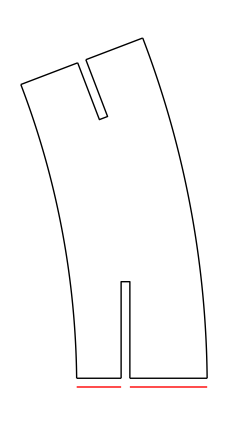

```mathematica
(* radius function, must repeat over period of 0 to 1 and be 1 at 0 and 1 *)
r[t_] := (90+Cos[5*2π t])/91;
r[t_] := (90+Cos[3*2π t])/91;
r[t_] := 1;
ri[t_] := r[t];
ro[t_] := r[t];
triangle[t_] := Abs[2(t-Floor[t+1/2])];
(*ri[t_] := -triangle[10t]/30+1;
ro[t_] := triangle[12t]/30+1;*)
α1 = ArcSin[sweep/inner]; (* amount to back off on inner part *)
α2 = ArcSin[sweep/outer]; (* amount to back off on outer part *)
Show[Graphics[{
Red,
Line[{{inner,0},{hexDist,0}}],Line[{{hexDist+gap,0},{outer,0}}],

Black,
(* top and bottom boundaries *)
Line[{{inner,sweep},{hexDist,sweep}}],Line[{{hexDist+gap,sweep},{outer,sweep}}],

Line[{(inner){Cos[angle],Sin[angle]},(sqDist){Cos[angle],Sin[angle]}}],
Line[{(sqDist+gap){Cos[angle],Sin[angle]},(outer){Cos[angle],Sin[angle]}}],

(* outer and inner boundaries *)
Line[Table[(inner)ri[(t-α1)/(angle-α1)]{Cos[t],Sin[t]},{t,α1,angle,(angle-α1)/100}]],
Line[Table[(outer)ro[(t-α2)/(angle-α2)]{Cos[t],Sin[t]},{t,α2,angle,(angle-α2)/100}]],

(* notches *)
Line[{{hexDist,sweep},{hexDist,hexLeft},{hexDist+gap,hexLeft},{hexDist+gap,sweep}}],
Rotate[
Line[{{sqDist,0},{sqDist,-sqLeft},{sqDist+gap,-sqLeft},{sqDist+gap,0}}],
angle,{0,0}
]
}]]
```

```mathematica
connectorBoundary :=Simplify[Partition[Flatten[
(* lower edge *)
{{inner,sweep},{hexDist,sweep},
(* gap *)
{hexDist,hexLeft},{hexDist+gap,hexLeft},{hexDist+gap,sweep},

(* outer boundary *)
Table[(outer)ro[(t-α2)/(angle-α2)]{Cos[t],Sin[t]},{t,α2,angle,(angle-α2)/50}],

(* gap *)
rot[{sqDist+gap,0}],rot[{sqDist+gap,-sqLeft}],rot[{sqDist,-sqLeft}],
(* rest of edge *)
(sqDist){Cos[angle],Sin[angle]},

(* inner boundary *)
Table[(inner)ri[(t-α1)/(angle-α1)]{Cos[t],Sin[t]},{t,angle,α1,-(angle-α1)/50}]
}],2]];
Graphics[Line[connectorBoundary]]
```

-Graphics-

```mathematica
connector3D := connectorBoundary /. {x1_,y1_}->{x1,y1,0};
Graphics3D[Polygon[thicken[connector3D,thickness]]]
```

-Graphics3D-

## Final assembly

```mathematica
(* thie final piece, centered nicely *)
cPiece := thicken[#-thickness/2&/@connector3D,thickness];
Graphics3D[Polygon[cPiece]]
```

-Graphics3D-

```mathematica
(* The geometric shape *)
shapeC := Polygon[cPiece]
```

```mathematica
(* three at a time *)
threeC := {shapeC,
Rotate[shapeC,2π/3,{1,0,0},{0,0,0}],
Rotate[shapeC,4π/3,{1,0,0},{0,0,0}]};
Graphics3D[threeC]
```

-Graphics3D-

```mathematica
(* polygon centers  *)
polyCenters = N[centroid /@ pg];
```

```mathematica
Length[polyCenters]
```

50

```mathematica
(* shortest distance between hex and square centroids *)
minDist = Simplify[Norm[(#[[1]]-#[[2]])&[(centroid /@ pg2)]]]
```

√(5+√5)

```mathematica
(* For each hex centroid, find all square centroids within minDist *)
matchHexCentroids[hexCentroid_] := Select[centroid /@ squares,Norm[#-hexCentroid]<=minDist+0.1&]
```

```mathematica
matchHexCentroids[centroid[hexes[[1]]]] // N
```

{{2.30902,-3.73607,6.04508},{-2.30902,-3.73607,6.04508},{0.,0.,7.47214}}

```mathematica
(* show each hex centroid, and then each matching set of squares *)
matches = {centroid[#],matchHexCentroids[centroid[#]]}&/@hexes;
```

```mathematica
(* given a match (a hexcentroid and the three surrounding square centroids)
 create the three connectors that go there *)
matchC[match_] := Module[{a1={1,0,0},a2={Cos[angle],Sin[angle],0},b1,b2,m1,m2,ang,θ,p1,p2,p3},
b1=match[[1]];
b1/=Norm[b1]; (* the hex centroid *)
b2 = match[[2,1]];
b2/=Norm[b2]; (* one of the square centroids *)
m1 = RotationMatrix[{a1,b1}]; (* map a1 to b1 *)
m2 = RotationMatrix[θ,{1,0,0}]; (* rotate here until a2 close to b2 *)
ang=θ/.NMinimize[Norm[m1.m2.a2-b2],θ][[2]];
m2 = RotationMatrix[ang,{1,0,0}]; (* final rotation piece *)
(* three pieces *)
p1 = m1.m2.#&/@#&/@cPiece;
p2 = m1.m2.RotationMatrix[2π/3,{1,0,0}].#&/@#&/@cPiece;
p3 = m1.m2.RotationMatrix[4π/3,{1,0,0}].#&/@#&/@cPiece;
Return[Flatten[{p1,p2,p3},1]]
]
```

```mathematica
Graphics3D[Polygon[matchC[matches[[1]]]]]
```

-Graphics3D-

```mathematica
(* all matching pieces *)
placedConnectors = matchC /@ matches;
```

```mathematica
(* notched pieces *)
notchedSquares = notch[#,gap,sqCut]&/@squares;
notchedHexes = notch[#,gap,hexCut]&/@hexes;
```

```mathematica
Graphics3D[{
LightBlue,Polygon/@ placedConnectors,
Red,Polygon /@ thicken[#,thickness]&/@notchedSquares,
Green,Polygon/@thicken[#,thickness]&/@notchedHexes
}]
```

-Graphics3D-

## Final geometry intersection check

```mathematica
Graphics3D[{
LightBlue,Polygon/@ placedConnectors[[{2,5}]],
Red,Polygon /@ thicken[#,thickness]&/@notchedSquares[[{7}]],
Green,Polygon/@thicken[#,thickness]&/@notchedHexes[[{2,5}]]
}]
```

-Graphics3D-

## Logo

```mathematica
?FontFamily
```

## Laser Template

```mathematica
(* each template is a list of lines *)
```

```mathematica
(* given the points defining an outside of a polygon, convert to a list of lines *)
polyToLines[lst_] := Transpose[Join[{lst},{RotateLeft[lst]}]]
```

```mathematica
hexagon = polyToLines[notch[Table[sideLength{Cos[a],Sin[a],0},{a,π/6,2π,2π/6}],gap,hexCut] /. {x1_,y1_,z1_}->{x1,y1}];
```

```mathematica
square = polyToLines[notch[Table[sideLength/√2{Cos[a],Sin[a],0},{a,π/4,π/4+2π-1/100,2π/4}],gap,sqCut] /. {x1_,y1_,z1_}->{x1,y1}];
```

```mathematica
connector = polyToLines[connectorBoundary];
```

```mathematica
translate[lines_,delta_] := lines /. {{x1_,y1_},{x2_,y2_}}->{{x1+delta[[1]],y1+delta[[2]]},{x2+delta[[1]],y2+delta[[2]]}}
```

```mathematica
rotate[lines_,angle_] := Block[{mat = {{Cos[angle],-Sin[angle]},{Sin[angle],Cos[angle]}}},
lines /. {{x1_,y1_},{x2_,y2_}}->{mat.{x1,y1},mat.{x2,y2}}
]
```

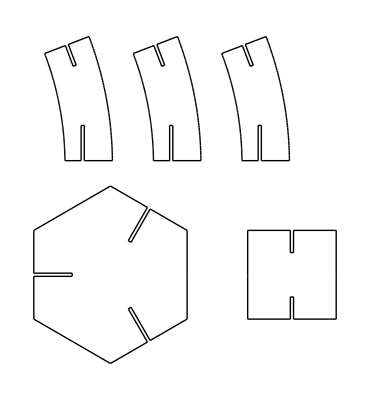

```mathematica
testTemplate = Partition[Partition[Flatten[Join[translate[square,{2*sideLength+1/10,0}],
hexagon,
Table[translate[ connector,{-8+2i,5/2}],{i,0,2}]
]],2],2];
Graphics[Line /@ testTemplate]
```

```mathematica
Tally[Length/@pg]
```

{{6,20},{4,30}}

Need 20 hexes, 30 squares, and 3*hexes = 60 connectors

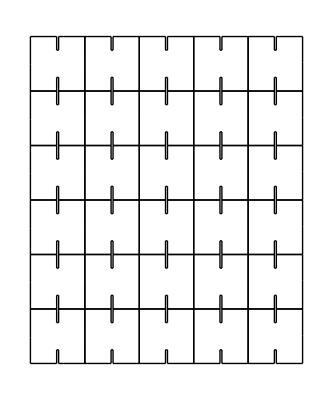

```mathematica
squareTemplate =Partition[Partition[Flatten[Table[translate[square,{i,j}],{i,0,4*sideLength,sideLength},{j,0,5sideLength,sideLength}]],2],2]; 
Graphics[Line/@squareTemplate]
```

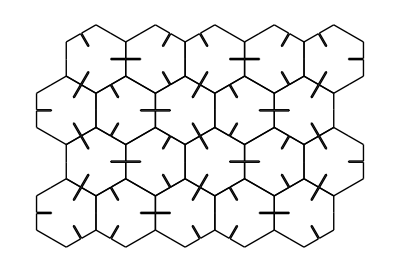

```mathematica
hexTemplate = Partition[Partition[Flatten[Table[translate[rotate[hexagon,Mod[j+i,2,1]π/3],{i √3 sideLength+√3 Mod[j,2],j 3/2 * sideLength}],{i,0,4},{j,0,3}]],2],2];
Graphics[Line /@ hexTemplate]
```

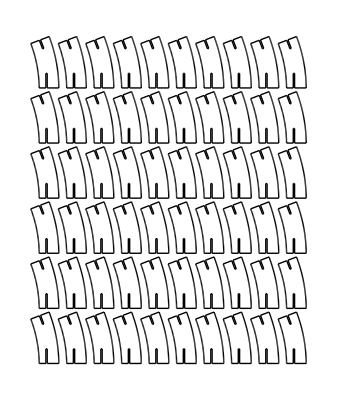

```mathematica
connectorTemplate = Partition[Partition[Flatten[
Table[translate[connector,{i 3/4 sideLength,j 3/2 sideLength}],{i,0,9},{j,0,5}]],2],2];
Graphics[Line/@connectorTemplate]
```

### Since Mathematica fails on the DXF export of these (only outputs one closed contour per item) I export the list of line values and use a C # program that removes dups, 0 length lines, and merges lines as possible, outputting the DXF files.

```mathematica
Export[NotebookDirectory[]<>"testData.txt",N[Flatten[testTemplate]]]
```

/Users/bob/Documents/Firefly Art/testData.txt

```mathematica
Export[NotebookDirectory[]<>"squareData.txt",N[Flatten[squareTemplate]]]
```

/Users/bob/Documents/Firefly Art/squareData.txt

```mathematica
Export[NotebookDirectory[]<>"hexData.txt",N[Flatten[hexTemplate]]]
```

/Users/bob/Documents/Firefly Art/hexData.txt

```mathematica
Export[NotebookDirectory[]<>"connectorData.txt",N[Flatten[connectorTemplate]]]
```

/Users/bob/Documents/Firefly Art/connectorData.txt

```mathematica
(* Check the imports, which come as 3D *)
```

```mathematica
Import[NotebookDirectory[]<>"test.dxf"]
```

Import::nffil: File /Users/bob/Documents/Firefly Art/test.dxf not found during Import.

$Failed

```mathematica
Import[NotebookDirectory[]<>"squares.dxf"]
```

Import::nffil: File /Users/bob/Documents/Firefly Art/squares.dxf not found during Import.

$Failed

```mathematica
Import[NotebookDirectory[]<>"hexes.dxf"]
```

Import::nffil: File /Users/bob/Documents/Firefly Art/hexes.dxf not found during Import.

$Failed

```mathematica
Import[NotebookDirectory[]<>"connectors.dxf"]
```

Import::nffil: File /Users/bob/Documents/Firefly Art/connectors.dxf not found during Import.

$Failed